```mathematica
(* cost of MV sumcheck, relative to the size|H| of the n-dimensional hypercube
*)
ClearAll@sumcheck;
sumcheck[n_,d_,numVars_,{Qm_,Qs_,Qa_}]:=
(1 - 1/2^(n)) * {d*numVars + (d+1) * Qm, numVars + (d + 1) * Qs, d*numVars + (d+1)*(Qa + 1)}
```

```mathematica
(* From Berstein and Lange, 2007, Analysis of EC single scalar multiplication
costPerScalarBit = 8; (* InvEdwards coordinates *)
costPerScalarMul = 8*255
costPippengerPerScalar = costPerScalarMul/12 (* 1 / log|H|, with |H|=2^12 *) 
*)

(* 
Cost of Pippenger in terms of field multiplications.
Based on Marcin single-threaded benchmarks of Pippenger
https://github.com/Orbis-Tertius/Orbis/issues/97
*)


instanceSizes = Range[12,18];
benchesPippenger= {46.010, 82.382, 153.67, 279.35, 522.13, 1003.4, 1869.5}; (* for N=12, 13,..., 18*)
benchesFieldMul = {21.110, 42.315, 84.777, 169.70, 339.25, 679.27, 1360.6}; (* for 2^8 * N *)
equivalentMuls = benchesPippenger/benchesFieldMul * 2^8
```

{557.961,498.4,464.035,421.412,394.002,378.157,351.751}

```mathematica
maxM = 200;
domainSize = 12;
costPippengerPerScalar = equivalentMuls[[Position[instanceSizes, domainSize]//Flatten//First]]
```

557.961

## Based on the logarithmic derivative

### small number of columns

```mathematica
arithComp = {4M + 1,1,M+1};
costsumcheck = sumcheck[n, M+3,M+4, arithComp ]/(1 - 1/2^n)//Simplify
cost = costsumcheck+ {7, 1, 2M+1}//Simplify
```

{16+24 M+5 M^2,2 (4+M),20+13 M+2 M^2}

{23+24 M+5 M^2,9+2 M,21+15 M+2 M^2}

### large number of columns (old)

```mathematica
(*
The old variant for M=2^m number of columns.
arithComp = {4,1,2};
costsumcheckLargeM = M * sumcheck[n+m, 4, 5, arithComp]/(1 - 1/2^(n+m))//Simplify
costLargeM = costsumcheckLargeM + M * {4, 0, 2}//Simplify
*)
```

### large number of columns

```mathematica
arithComp = {2(M+2),M+2,2M};
costsumcheckLargeM = sumcheck[n, 3, 2(M+2), arithComp]/(1 - 1/2^n)//Simplify
costLargeM = costsumcheckLargeM + {3(M+1)+1, 0, M+2}//Simplify
```

{14 (2+M),6 (2+M),2 (8+7 M)}

{32+17 M,6 (2+M),3 (6+5 M)}

### break even point

{726.501+24 M+5 M^2,712.501+2 M,724.501+15 M+2 M^2}

{32+17 M+351.751 (2+M),357.751 (2+M),351.751 (2+M)+3 (6+5 M)}

{{M→-0.0260959},{M→68.9762}}

68

3.01603

10

1466.5

1.5

{2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43}

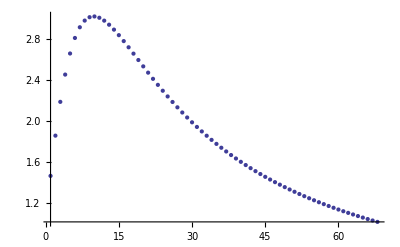

```mathematica
costWithComm = cost + costPippengerPerScalar*2
costWithCommLarge = costLargeM + costPippengerPerScalar*(M+2)

(* break even point with linear strategy *)
sol = NSolve[costWithComm[[1]] == costWithCommLarge[[1]],M]
breakEven = M /. sol // Last//Floor

(* maximum speedup *)

ratio = Table[costWithCommLarge[[1]]/costWithComm[[1]]/.{M->x},
{x,1, breakEven}];
max = Max@ratio;
max//N
best = Position[ratio,max]//Flatten//First
costWithComm[[1]]/. {M-> best}
(* range for 0.8 of the maximum speedup *)
threshold = 1.5
Position[(#≥threshold)&/@ratio,True]//Flatten

ListPlot[ratio,PlotRange->All]
```

### Best strategy

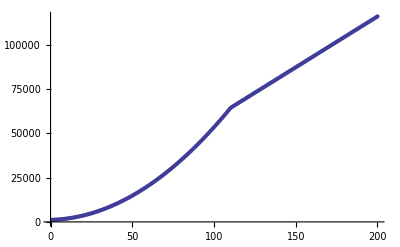

```mathematica
bestCostWithComm = Join[
Table[costWithComm[[1]]/.{M->x},{x,1,breakEven}],
Table[costWithCommLarge[[1]]/.{M->x},{x,breakEven+1,maxM}]
];
ListPlot[bestCostWithComm]
```

## Based on the univariate strategy

### small number of columns

```mathematica
arithComp = {2(M+1)+3,2,1};
costsumcheckUV = sumcheck[n, M+3, 2M+6, arithComp]/(1 - 1/2^n)//Simplify
costUV = costsumcheckUV+ {2(M+1)+(2M+4)+2, 0, 3M+5}//Simplify
```

{38+25 M+4 M^2,14+4 M,2 (13+7 M+M^2)}

{46+29 M+4 M^2,14+4 M,31+17 M+2 M^2}

### large number of columns

```mathematica
arithComp = {5,2,1};
costsumcheckUVlarge = (M+1) * sumcheck[n+m, 3, 6, arithComp]/(1 - 1/2^(n+m))//Simplify
costUVlarge = costsumcheckUVlarge+ (M+1){7, 0, 4}//Simplify
```

{38 (1+M),14 (1+M),26 (1+M)}

{45 (1+M),14 (1+M),30 (1+M)}

### break even point

{46+29 M+4 M^2+557.961 (2+M),14+4 M+557.961 (2+M),31+17 M+2 M^2+557.961 (2+M)}

{1160.92 (1+M),1129.92 (1+M),1145.92 (1+M)}

{{M→0.0017423},{M→143.489}}

143

1.71936

11

1.37548

{2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,61,62,63}

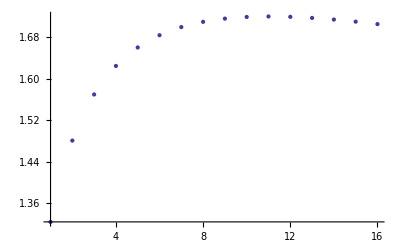

1.70902

6113.61

```mathematica
costWithCommUV = costUV + costPippengerPerScalar * (M+2)
costWithCommUVlarge = costUVlarge + costPippengerPerScalar * 2*(M+1)

(* break even point with linear strategy *)
sol = NSolve[costWithCommUV[[1]] == costWithCommUVlarge[[1]],M]
breakEvenUV = M /. sol // Last//Floor

(* maximum speedup *)
ratio = Table[costWithCommUVlarge[[1]]/costWithCommUV[[1]]/.{M->x},
{x,1, breakEvenUV}];
max = Max@ratio;
max//N
best = Position[ratio,max]//Flatten//First


(* range for 0.8 of the maximum speedup *)
max * 0.80
Position[(#≥max*0.80)&/@ratio,True]//Flatten

ListPlot[ratio[[1;;16]],PlotRange->All]
ratio[[8]]
costWithCommUV[[1]]/.{M->8}
```

### best strategy

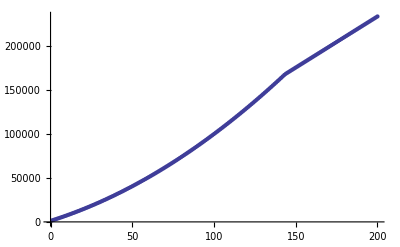

```mathematica
bestCostWithCommUV = Join[
Table[costWithCommUV[[1]]/.{M->x},{x,1,breakEvenUV}],
Table[costWithCommUVlarge[[1]]/.{M->x},{x,breakEvenUV+1,maxM}]
];
ListPlot[bestCostWithCommUV]
```

## Comparison

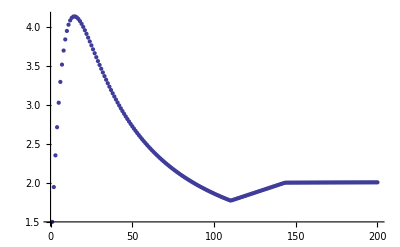

```mathematica
ListPlot[bestCostWithCommUV/bestCostWithComm]
```

```mathematica
(* the number of muls for optimal batch size M *)
dom={12,14,16,18};
logDer ={{13,2296},{12,1959},{11,1680},{10,1466}};
plookup={{8,6113},{8,5174},{8,4474},{8,4052}};
logDerPerCol= #[[2]]/#[[1]]&/@logDer //N
plookupPerCol= #[[2]]/#[[1]]&/@plookup //N
plookupPerCol/logDerPerCol
```

{176.615,163.25,152.727,146.6}

{764.125,646.75,559.25,506.5}

{4.32649,3.96172,3.66176,3.45498}